```mathematica
Series[(√(L^2+y^2)-L0)^2,{y,0,4}]
```

(√(L^2)-L0)^2+((√(L^2)-L0) y^2)/(√(L^2))+(√(L^2) L0 y^4)/(4 L^4)+O[y]^5

```mathematica
Expand[(L(1+1/2 y^2/L^2)-L0)^2]
```

L^2-2 L L0+L0^2+y^2-(L0 y^2)/L+y^4/(4 L^2)

```mathematica
(√(L^2+y^2)-L0)^2//Expand
```

L^2+L0^2+y^2-2 L0 √(L^2+y^2)

```mathematica
Series[√(1+x),{x,0,4}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+O[x]^5

```mathematica
U[y_]:=k(1-L0/L)y^2+(k L0)/(4 L^3)y^4
```

```mathematica
-D[U[s+y0 Cos[ω t]],s]/.(s->y-y0 Cos[ω t])//Simplify
```

-(k y (2 L^3-2 L^2 L0+L0 y^2))/L^3

```mathematica
FullSimplify[Integrate[(s+y0 Cos[ t])^2,{t,a,b}]/(b-a),Assumptions->a!=b&&{a,b}∈Reals&&a!=0&&b!=0]
```

((a-b) (2 s^2+y0^2)+y0 (4 s+y0 Cos[a]) Sin[a]-y0 (4 s+y0 Cos[b]) Sin[b])/(2 (a-b))

```mathematica
D[√(ωp^2+c^2 k^2),k]/.k->ω/c √(1-ωp^2/ω^2)
```

```mathematica
(c ω √(1-ωp^2/ω^2))/(√(ωp^2+ω^2 (1-ωp^2/ω^2)))//Simplify
```

```mathematica
c √(1-ωp^2/ω^2)
```

```mathematica
u={1,1}/(√2);
A=Outer[Times,u,u]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
A.A.A.A
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
up=Transpose@{u};
up.Transpose@up//MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1)

```mathematica
MatrixExp[Outer[Times,u,u]]
```

{{1/5 (4+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5)},{1/5 (-1+ⅇ^5),1/5 (4+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5)},{1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (4+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5)},{1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (4+ⅇ^5),1/5 (-1+ⅇ^5)},{1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (-1+ⅇ^5),1/5 (4+ⅇ^5)}}

```mathematica
(*q=2*)
sigma[i]∈
```

```mathematica
H=-(3J)/2(KroneckerDelta[sigma[1],sigma[2]])
```

```mathematica
MatrixExp[2IdentityMatrix[2]+A]//MatrixForm
```

(ⅇ^2/2+ⅇ^3/2 | -ⅇ^2/2+ⅇ^3/2
-ⅇ^2/2+ⅇ^3/2 | ⅇ^2/2+ⅇ^3/2)

```mathematica
uv=Table[1/√5,{i,1,5}];
B=Outer[Times,uv,uv];
c=B-Exp[β J]IdentityMatrix[5];
```

```mathematica
H=B+(Exp[β J]-1)IdentityMatrix[5]
```

{{ⅇ^(J β),1,1,1,1},{1,ⅇ^(J β),1,1,1},{1,1,ⅇ^(J β),1,1},{1,1,1,ⅇ^(J β),1},{1,1,1,1,ⅇ^(J β)}}

```mathematica
MatrixLog[H]//MatrixForm
```

(4/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)]
-1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | 4/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)]
-1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | 4/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)]
-1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | 4/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)]
-1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | -1/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)] | 4/5 Log[-1+ⅇ^(J β)]+1/5 Log[4+ⅇ^(J β)])

```mathematica
B//MatrixForm
```

(1/5 | 1/5 | 1/5 | 1/5 | 1/5
1/5 | 1/5 | 1/5 | 1/5 | 1/5
1/5 | 1/5 | 1/5 | 1/5 | 1/5
1/5 | 1/5 | 1/5 | 1/5 | 1/5
1/5 | 1/5 | 1/5 | 1/5 | 1/5)

```mathematica
uv.uv
```

1

```mathematica
s1={1,0};
s2={-1/2,√3/2};
s3={-1/2,-√3/2};
s1.s1
s2.s2
s3.s3
s1.s2
s1.s3
s2.s3
```

1

1

1

-1/2

-1/2

-1/2

```mathematica
a=Table[1,{i,1,5}]
A=Outer[Times,a,a];
```

{1,1,1,1,1}

```mathematica
A.A
```

{{5,5,5,5,5},{5,5,5,5,5},{5,5,5,5,5},{5,5,5,5,5},{5,5,5,5,5}}

```mathematica
Binomial[x,x]
```

1

```mathematica
D[-(n k)/3((2m+1)Log[(2m+1)/3]+2(1-m)Log[(1-m)/3]),m]
```

-1/3 k n (-2 Log[(1-m)/3]+2 Log[1/3 (1+2 m)])

```mathematica
D[n(-J z m^2+1/(3β)((1+2m)Log[(2m+1)/3]+2(m-1)Log[(1-m)/3])),{m,2}]
```

n (-2 J z+(-4/(1-m)-(2 (-1+m))/(1-m)^2+4/(1+2 m))/(3 β))

```mathematica
Simplify[n (-2 J z+(-4/(1-m)-(2 (-1+m))/(1-m)^2+4/(1+2 m))/(3 β))]
```

-(2 n (1-3 J z β+6 J m^2 z β-m (4+3 J z β)))/(3 (-1+m) (1+2 m) β)

```mathematica
Simplify[n (-2 J m z+(2-(2 (-1+m))/(1-m)+2 Log[(1-m)/3]+2 Log[1/3 (1+2 m)])/(3 β))]
```

(2 n (2-3 J m z β+Log[(1-m)/9]+Log[1+2 m]))/(3 β)

```mathematica
D[-2J z m+2/3 k T Log[(2m+1)/(1-m)],m]//FullSimplify
```

(2 k T)/(1+m-2 m^2)-2 J z

```mathematica
Simplify[(2 k (1-m) (2/(1-m)+(1+2 m)/(1-m)^2) T)/(3 (1+2 m))-2 J z]
```

(-2 k T+2 J (1+m-2 m^2) z)/((-1+m) (1+2 m))

```mathematica
2/(1+m-2 m^2)//Apart
```

-2/(3 (-1+m))+4/(3 (1+2 m))

```mathematica
Plot3D[-m^2+T/3((1+2m)Log[(2m+1)/3]+2(m-1)Log[(1-m)/3]),{m,-1/2,1},{T,0,1}]
```

-Graphics3D-

```mathematica
F=n(-J z m^2+(k T)/3((1+2m)Log[(1+2m)/3]+2(1-m)Log[(1-m)/3]));
nice={n->1,z->1,J->1,k->1};
D[F,m]
D[F,m,m]
```

n (-2 J m z+1/3 k T (-2 Log[(1-m)/3]+2 Log[1/3 (1+2 m)]))

n (1/3 k (2/(1-m)+4/(1+2 m)) T-2 J z)

```mathematica
F/.nice
```

-m^2+1/3 T (2 (1-m) Log[(1-m)/3]+(1+2 m) Log[1/3 (1+2 m)])

```mathematica
free=F/.nice;
Manipulate[Plot[free/.T->t,{m,-1/2,1},AxesLabel->{"m","F"}],{{t,5},0,1.2,0.01}]
```

```mathematica
Table[NSolve[D[free/.T->t,m]==0,m]
```

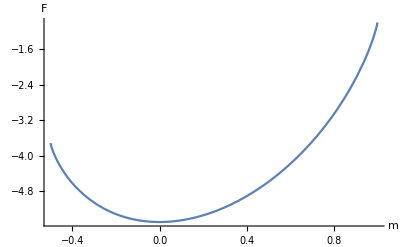

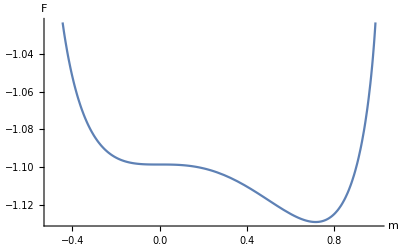

```mathematica
fig4=Plot[free/.T->5,{m,-1/2,1},AxesLabel->{"m","F"}]
fig5=Plot[free/.T->1,{m,-1/2,1},AxesLabel->{"m","F"}]
```

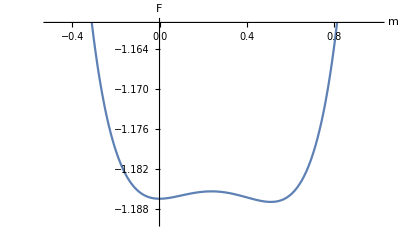

```mathematica
fig7=Plot[free/.T->1.08,{m,-1/2,1},AxesLabel->{"m","F"},PlotRange->{-1.19,-1.16}]
```

```mathematica
Export["~/school/SP23/Quals/Spring/figs/FvmTsamemin.png",fig7]
```

~/school/SP23/Quals/Spring/figs/FvmTsamemin.png

```mathematica
ParallelTable[{T,Abs[m]/.NMinimize[free/.T->t,m][[2]]},{t,0.5,1.5,0.001}]
```

NMinimize::nrnum: The function value -0.822617-0.344583 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.832358-0.369393 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.842099-0.394203 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.85184-0.419013 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.822888-0.345272 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.832629-0.370082 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.842369-0.394892 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.85211-0.419702 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.823158-0.345961 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.832899-0.370771 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.84264-0.395581 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.852381-0.420391 ⅈ is not a real number at {m} = {-0.829053}.

General::stop: Further output of NMinimize::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::nrnum: The function value -0.861581-0.443823 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.871321-0.468633 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.881062-0.493443 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.890803-0.518253 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.861851-0.444512 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.871592-0.469322 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.881333-0.494132 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.891074-0.518942 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.862122-0.445201 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.871862-0.470011 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.881603-0.494821 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.891344-0.519631 ⅈ is not a real number at {m} = {-0.829053}.

General::stop: Further output of NMinimize::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::nrnum: The function value -0.900544-0.543063 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.910285-0.567873 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.920025-0.592683 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.929766-0.617493 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.900814-0.543752 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.910555-0.568562 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.920296-0.593372 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.930037-0.618182 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.901085-0.544441 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.910826-0.569251 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.920567-0.594061 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.930307-0.618871 ⅈ is not a real number at {m} = {-0.829053}.

General::stop: Further output of NMinimize::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::nrnum: The function value -0.939507-0.642303 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.949248-0.667113 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.958989-0.691923 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.96873-0.716733 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.939778-0.642992 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.949518-0.667802 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.959259-0.692612 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.969-0.717422 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.940048-0.643681 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.949789-0.668491 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.95953-0.693301 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.969271-0.718111 ⅈ is not a real number at {m} = {-0.829053}.

General::stop: Further output of NMinimize::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::nrnum: The function value -0.97847-0.741543 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.988211-0.766353 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.997952-0.791163 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.00769-0.815973 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.978741-0.742232 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.988482-0.767042 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.998223-0.791852 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.00796-0.816662 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -0.979012-0.742921 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.988752-0.767731 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -0.998493-0.792541 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.00823-0.817351 ⅈ is not a real number at {m} = {-0.829053}.

General::stop: Further output of NMinimize::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::nrnum: The function value -1.01743-0.840782 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.02717-0.865592 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.03664-0.889713 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.04611-0.913834 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nrnum: The function value -1.0177-0.841472 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.02745-0.866282 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.03692-0.890402 ⅈ is not a real number at {m} = {-0.829053}.

NMinimize::nrnum: The function value -1.04639-0.914523 ⅈ is not a real number at {m} = {-0.829053}.

ReplaceAll::reps: {m} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
Manipulate[Plot[(2m+1)/(1-m)-Exp[(3 m)/T],{m,-1/2,1}],{T,0.1,1.5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

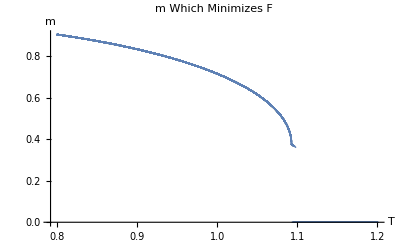

```mathematica
Sols=ParallelTable[{t,m/.FindRoot[2m+1-(1-m)Exp[(3 m)/T]/.T->t,{m,1.1}]},{t,0.8,1.2,0.00001}]//Quiet;
fig6=ListPlot[Sols,AxesLabel->{"T","m"},PlotLabel->"m Which Minimizes F"]
```

```mathematica
Export["~/school/SP23/Quals/Spring/figs/mvt.png",fig6]
Export["~/school/SP23/Quals/Spring/figs/FvmT1.png",fig5]
Export["~/school/SP23/Quals/Spring/figs/FvmT5.png",fig4]
```

~/school/SP23/Quals/Spring/figs/mvt.png

~/school/SP23/Quals/Spring/figs/FvmT1.png

~/school/SP23/Quals/Spring/figs/FvmT5.png

```mathematica
Export["~/school/SP23/Quals/Spring/figs/phasegroup.png",fig]
```

```mathematica
free/.T->10
```

-m^2+10/3 (2 (1-m) Log[(1-m)/3]+(1+2 m) Log[1/3 (1+2 m)])

```mathematica
Simplify[-3/((-1+m) (1+2 m))]
```

3/(1+m-2 m^2)

```mathematica
Solve[(1-(k T)/(J z))+m-2 m^2==0,m]
```

{{m→1/4 (1-(√(-8 k T+9 J z))/(√J √z))},{m→1/4 (1+(√(-8 k T+9 J z))/(√J √z))}}

```mathematica
FullSimplify[Reduce[1/4 (1-(√(-8 k T+9 J z))/(√J √z))<0],Assumptions->k>0&&T>0&&J>0&&z>0]
FullSimplify[Reduce[1/4 (1+(√(-8 k T+9 J z))/(√J √z))<0],Assumptions->k>0&&T>0&&J>0&&z>0]
```

k T<J z

False

```mathematica
FullSimplify[Integrate[Cos[ω x]^3,{x,0,2π n/ω}],Assumptions->n∈Integers]/(2π n/ω)
```

0

```mathematica
(α+y0 Cos[ω t])^4//Expand
```

α^4+4 y0 α^3 Cos[t ω]+6 y0^2 α^2 Cos[t ω]^2+4 y0^3 α Cos[t ω]^3+y0^4 Cos[t ω]^4

```mathematica
Clear[A,B,c]
```

```mathematica
Solve[b+2c α^2==0,α]
```

{{α→-(ⅈ √b)/(√2 √c)},{α→(ⅈ √b)/(√2 √c)}}

```mathematica
FullSimplify[Reduce[k(1-L0/L)+(3k L0 y0^2)/(4 L^3)<0],Assumptions->k>0&&L>0&&L0>0&&L<L0&&y0>0]
FullSimplify[Reduce[(k L0)/(4 L^3)<0],Assumptions->k>0&&L>0&&L0>0&&L<L0&&y0>0]
```

y0<(2 L)/(√3)&&L0>(4 L^3)/(4 L^2-3 y0^2)

False

```mathematica
-(k(1-L0/L)+(3k L0 y0^2)/(4 L^3))/(2(k L0)/(4 L^3))//FullSimplify
```

```mathematica
FullSimplify[Reduce[2 L^2-(2 L^3)/L0-(3 y0^2)/2>0],Assumptions->k>0&&L>0&&L0>0&&L<L0&&y0>0&&y0>L]
```

3 y0<2 L √(3-(3 L)/L0)

```mathematica
(1/2 k(x-(L-L0))^2+1/2 k(x+(L-L0))^2)//Expand
```

k L^2-2 k L L0+k L0^2+k x^2

```mathematica
Clear[a,b,c]
```

```mathematica
Ueff=a+b α^2+c α^4;
D[Ueff,α,α]/.α->√(-b/(2c))
```

-4 b

```mathematica
2-4b=k
```

```mathematica
Solve[k==m ω^2,ω]
```

{{ω→-(√k)/(√m)},{ω→(√k)/(√m)}}

```mathematica
sUeff=A s^2+ B s^4
D[sUeff,s,s]/.s->√(-A/(2B))
```

A s^2+B s^4

-4 A

```mathematica
Curl[{0, B x,0},{x,y,z}]
```

{0,0,B}

```mathematica
fig1=Plot[{-x((x-2)+(x-2)^3),-Sin[100x]x((x-2)+(x-2)^3),x((x-2)+(x-2)^3)},{x,0,2},PlotStyle->{Red,Blue,Red},PlotLegends->{"Envelope","Modulation"}];
```

```mathematica
Export["~/school/SP23/Quals/Spring/figs/phasegroup.png",fig1]
```

~/school/SP23/Quals/Spring/figs/phasegroup.png

```mathematica
uv=Table[1,{i,1,5}]
```

{1,1,1,1,1}

```mathematica
M=Outer[Times,uv,uv];
M.M.M==5*5 M
```

True

```mathematica
Inverse[M]
```

Inverse::sing: Matrix {{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}} is singular.

Inverse[{{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}]

```mathematica
A *M//Flatten//Length
```

25

```mathematica
A*IdentityMatrix[5]
```

{{A,0,0,0,0},{0,A,0,0,0},{0,0,A,0,0},{0,0,0,A,0},{0,0,0,0,A}}

```mathematica
q((e^α+q-1)^n-(e^α-1)^n)+q(e^α-1)^n
```

(-1+e^α)^n q+q (-(-1+e^α)^n+(-1+e^α+q)^n)

```mathematica
Simplify[(-1+e^α)^n q+q (-(-1+e^α)^n+(-1+e^α+q)^n)]
```

q (-1+e^α+q)^n

```mathematica
eff=(a+b α^2+c α^4)/.{a->k(L-L0)^2+(k y0^2)/2(1-L0/L)+(3k L0 y0^4)/(32 L^3),b->k(1-L0/L)+(3k L0 y0^2)/(4 L^3),c->(k L0)/(4 L^3)}
```

{k→1,L→1,L0→2,y0→3}

k (L-L0)^2+1/2 k (1-L0/L) y0^2+(3 k L0 y0^4)/(32 L^3)+(k (1-L0/L)+(3 k L0 y0^2)/(4 L^3)) α^2+(k L0 α^4)/(4 L^3)

```mathematica
(k(1-L0/L)+(3k L0 y0^2)/(4 L^3))/(2(k L0)/(4 L^3))//Simplify
```

```mathematica
-2 L^2+(2 L^3)/L0+(3 y0^2)/2/.{k->1,L->1,L0->2,y0->0.1}
 y0^2<4/3(L^2-L^3/L0)
```

-0.985

y0^2<4/3 (L^2-L^3/L0)

```mathematica
4/3(L^2-L^3/L0)/.rules
```

2/3

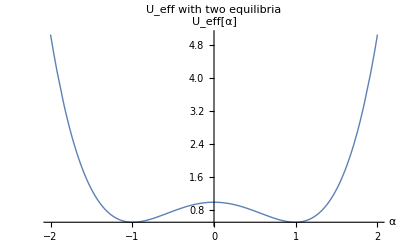

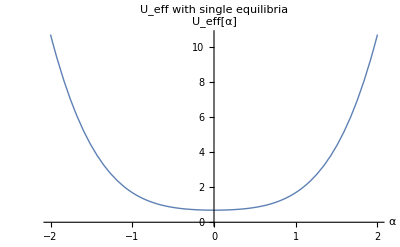

```mathematica
rules1={k->1,L->1,L0->2,y0->0.1};
fig2=Plot[eff/.rules1,{α,-2,2},PlotLabel->"U_eff with two equilibria",AxesLabel->{"α","U_eff[α]"},PlotStyle->Thick]
rules2={k->1,L->1,L0->2,y0->1};
fig3=Plot[eff/.rules2,{α,-2,2},PlotLabel->"U_eff with single equilibria",AxesLabel->{"α","U_eff[α]"},PlotStyle->Thick]
```

```mathematica
Export["~/school/SP23/Quals/Spring/figs/spm.png",fig2]
Export["~/school/SP23/Quals/Spring/figs/s0.png",fig3]
```

~/school/SP23/Quals/Spring/figs/spm.png

~/school/SP23/Quals/Spring/figs/s0.png